```mathematica
2+3
```

5

```mathematica
N[13/3]
```

4.33333

```mathematica
N[Pi]
```

3.14159

```mathematica
N[Pi,10]
```

3.141592654

```mathematica
promenna1 = 1
```

1

```mathematica
promenna2 = 2/3
```

2/3

```mathematica
2^5
```

32

```mathematica
√5
```

√5

```mathematica
√2//N
```

1.41421

```mathematica
ⅇ//N
```

2.71828

```mathematica
1,5
```

Syntax::tsntxi: "1, 5" is incomplete; more input is needed.""

Syntax::sntxi: Incomplete expression; more input is needed "".

```mathematica
piva = {Gambrinus, Plzen, Svijany, Staropramen}
```

{Gambrinus,Plzen,Svijany,Staropramen}

```mathematica
piva[[1]]
```

Gambrinus

```mathematica
First[piva]
```

Gambrinus

```mathematica
Last[piva]
```

Staropramen

```mathematica
piva[[-1]]
```

Staropramen

```mathematica
Gambrinus = {Desitka, Dvanactka, Cerne}
```

{Desitka,Dvanactka,Cerne}

```mathematica
piva[[1]][[3]]
```

Cerne

```mathematica
piva[[1,3]]
```

Cerne

```mathematica
matice1 = {{3,2,3}, {4,5,6}, {7,8,9}}
```

{{3,2,3},{4,5,6},{7,8,9}}

```mathematica
{{3,2,3},{4,5,6},{7,8,9}}
```

{{3,2,3},{4,5,6},{7,8,9}}

```mathematica
matice1 // MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
Det[matice1]
```

-6

```mathematica
{{3,2,3},{4,5,6},{7,8,9}}
```

{{3,2,3},{4,5,6},{7,8,9}}

```mathematica
x^2+5x+2
```

2+5 x+x^2

```mathematica
funkce = x^2+5x+2
```

2+5 x+x^2

```mathematica
x=1
```

1

```mathematica
funkce
```

8

```mathematica
x=2
```

2

```mathematica
funkce
```

16

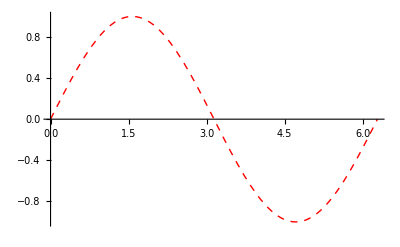

```mathematica
Plot[Sin[x], {x, 0, 2 Pi}, PlotStyle -> {Red, Thick, Dashed}]
```

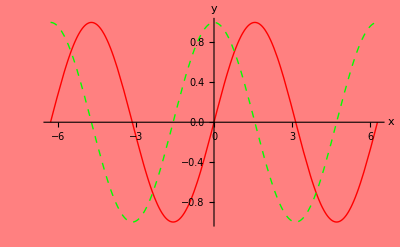

```mathematica
Plot[{Sin[x], Cos[x]}, {x, -2Pi, 2Pi}, PlotStyle -> {{Red, Thick}, {Green,Dashed}}, AxesLabel-> {"x","y"}, Background -> Pink, AxesStyle -> Blue]
```

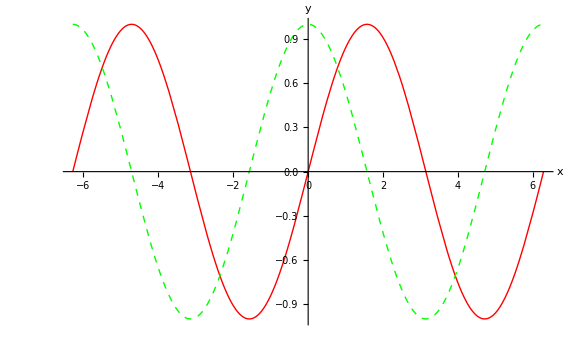

```mathematica
Show[%46,ImageSize->Large]
```

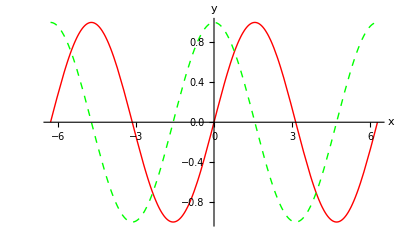

```mathematica
Show[%47,ImageSize->Tiny]
```

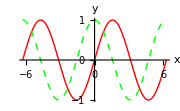

```mathematica
Show[%48,ImageSize->Small]
```

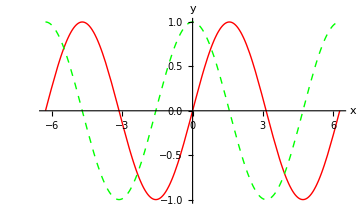

```mathematica
Show[%49,ImageSize->Medium]
```

```mathematica
Solve[2x-1==5, x]
```

Solve::ivar: 2 is not a valid variable.

Solve[False,2]

```mathematica
ClearAll[x]
```

```mathematica
?x
```

Global`x

```mathematica
Solve[2x-1==5, x]
```

```mathematica
{{x->3}}
```

{{x→3}}

```mathematica
Solve[x^2+6x-2==15, x]//N
```

{{x→-8.09902},{x→2.09902}}

```mathematica
Solve[{{2x+3y==6}, {5x-y==3}}, {x,y}]
```

Solve::naqs: {2\ x + 3\ y == 6} && {5\ x - y == 3} is not a quantified system of equations and inequalities.

```mathematica
Solve[{2 x+2 y==6,5 x-y==3},{x,y}]
```

{{x→1,y→2}}

```mathematica
rovnice = {2a+3b+c==1,a+b+2c==1,4a+b-c==3}
```

{2 a+3 b+c==1,a+b+2 c==1,4 a+b-c==3}

```mathematica
Solve[rovnice, {a,b,c}]
```

{{a→8/9,b→-1/3,c→2/9}}

```mathematica
vysledek = Solve[rovnice, {a,b,c}]
N[vysledek,3]
```

{{a→8/9,b→-1/3,c→2/9}}

{{a→0.889,b→-0.333,c→0.222}}

```mathematica
rovnice = {2a+3b+c==1,a+b+2c==1,4a+b-c==3};
vysledek = Solve[rovnice, {a,b,c}];
N[vysledek,3]
```

{{a→0.889,b→-0.333,c→0.222}}